# Vaccuum Rodrigo Study

## Tooling

```mathematica
SetAttributes[SP4,Orderless];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["cLTD`",NotebookDirectory[]<>"cLTD/cLTD.m"]
```

:::::::::::::::::::::::: cLTD ::::::::::::::::::::::::

Authors: Z. Capatti, V. Hirschi, D. Kermanschah, A. Pelloni, B. Ruijl

A Mathematica front end for cLTD [arxiv:2009.05509].

```mathematica
FORMPATH="/Users/vjhirsch/HEP_programs/form/bin/form";
```

```mathematica
SetOptions[cLTD,
	"WorkingDirectory"->NotebookDirectory[]<>"cLTD_work_dir/",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1]//TableForm
SetOptions[GeneratecLTDExpression,
	"WorkingDirectory"->NotebookDirectory[]<>"cLTD_work_dir/",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1];
```

loopmom→{k0,k1,k2,k3}
FORMpath→/Users/vjhirsch/HEP_programs/form/bin/form
tFORMpath→tform
WorkingDirectory→/Users/vjhirsch/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc/UV_derivatives_with_CFF_final/DOD1_example/cLTD_work_dir/
FORM_ID→1
FORMcores→1
OptimizationLVL→0
keep_FORM_script→False
EvalAll→False
NoNumerator→False
FORMsubs→False
stdLTD→False

```mathematica
ClearAll[GenerateLMBData];
GenerateLMBData[g_,OptionsPattern[{loopshift->{},externalshift->{}}]]:=Module[
{
edges=EdgeList[g],
props,
shift,
lmbEdgesIDs=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,cFFGetLMBEdges[g]}],
externals=cFFGetExternalEdges[g]
},
Association[Table[
props=(e/.DirectedEdge[_,_,props_]:>props);
shift=If[AllTrue[props["sig"]⟦1⟧,(#===0)&],
OptionValue[externalshift]
,
OptionValue[loopshift]
];
props["id"]-><|
"mass"->props["mass"],
"lmb_decomposition"->(
(
((props["sig"]⟦1⟧.Table[q[i],{i,lmbEdgesIDs}])
+(props["sig"]⟦2⟧.Table[q[(e/.DirectedEdge[_,_,props_]:>props)["id"]],{e,externals}]))/.shift
)
)
|>
,{e,edges}
]]
]
```

```mathematica
GetVirtualPropagators[g_]:=Module[
{
externalIDs=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,cFFGetExternalEdges[g]}]
},
Select[EdgeList[g],Not[MemberQ[externalIDs,(#/.DirectedEdge[_,_,props_]:>props)["id"]]]&]
]
```

```mathematica
GetVirtualPropagatorsIDs[g_]:=
Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,GetVirtualPropagators[g]}]
```

```mathematica
ExpandSP4[Num_]:=TensorExpand[Num/.{SP4[a_,b_]:>Cross[a/.{v_[i_]:>L[v[i]]},b/.{v_[i_]:>R[v[i]]}]}]/.{Cross[L[a_],R[b_]]:>SP4[a,b]}
```

```mathematica
NorExactZero[expr_]:=If[Evaluate[FullSimplify[expr]]===0,0,N[expr]]
```

```mathematica
ClearAll[ComputeSubtractionTermFromNormalized];
ComputeSubtractionTermFromNormalized[ct_,numerics_]:=Module[{lmbEdges,orkey,sortedEdgeIDs,reducedGraph,reducedGraphEdgeList,externalEdges,g},
lmbEdges=cFFGetLMBEdges[ct["graph"]];
g=ct["graph"];
externalEdges=cFFGetExternalEdges[g];
reducedGraph=GraphDifference[g,DirectedGraph[externalEdges]];
reducedGraphEdgeList=EdgeList[reducedGraph];
sortedEdgeIDs=Sort[Table[(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,GetVirtualPropagators[ct["graph"]]}]];
Association[SortBy[Table[
orkey=Table[
orientation["Orientation"][eID],
{eID,sortedEdgeIDs}
];
orkey->
1/(-1)^Length[reducedGraphEdgeList](-1)^Length[sortedEdgeIDs]/(-I)^Length[lmbEdges](1/λ)^3 EvalcFF[
ct["graph"],
{orientation},
numerics/.{Rule[k1,a_]->Rule[k1,1/λ a]},
Num->ct["num"],
DEBUG->False]
,
{orientation,ct["cFFexpr"]}],(#⟦1⟧)&]
]]
```

```mathematica
ClearAll[ComputeSubtractionTerm];
ComputeSubtractionTerm[ct_,numerics_,OptionsPattern[{UVEdgeIDs->{},UVTscalingReplacements->{},NumeratorFudge->None, DebugNumerator->False, UVRescaling->True}]]:=Module[
{orkey,sortedEdgeIDs,scalednumerics,ResPerOrientations,OSEReplacement,ShiftsReplacement,lmbEdges,externalEdges,g,orientationsForThisTerm,
signatures,momLabels,reducedGraph,reducedGraphEdgeList,processedNum, numForThisOrientation,internalOSEs,normalization,tmpKey,resForThisOrientation,OSEDef},
g=ct["graph"];
sortedEdgeIDs=Sort[Table[(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,GetVirtualPropagators[g]}]];
scalednumerics=If[OptionValue[UVRescaling],
numerics/.{Rule[k1,a_]->Rule[k1,1/λ a]},
numerics
];
momLabels=cFFGenerateMomentaLabels[g];
signatures=Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[g]}]];

lmbEdges=cFFGetLMBEdges[g];
externalEdges=cFFGetExternalEdges[g];
reducedGraph=GraphDifference[g,DirectedGraph[externalEdges]];
reducedGraphEdgeList=SortBy[EdgeList[reducedGraph],(Evaluate[(#/.{DirectedEdge[_,_,props_]:>props})]["id"])&];
ShiftsReplacement = Table[pE[iExt]:>Evaluate[ToExpression["p"<>ToString[iExt]<>"E"]],{iExt,Length[externalEdges]}]/.numerics;

processedNum=TensorExpand[ct["num"]/.{SP4[a_,b_]:>Cross[a/.{v_[i_]:>L[v[i]]},b/.{v_[i_]:>R[v[i]]}]}]/.{Cross[L[a_],R[b_]]:>SP4[a,b]};
processedNum=(processedNum/.{SP4[a_,b_]:>(a[0]*b[0]-a . b)})/.{q[i_][0]:>qE[i]};
Do[
processedNum=(((processedNum)/.{q[uveid]:>(signatures[uveid][[1]] . momLabels[[1]]+signatures[uveid][[2]] . momLabels[[2]])})/.Table[qE[(externalEdges[[iExt]]/.{DirectedEdge[_,_,props_]:>props})["id"]]:>Evaluate[pE[iExt]],{iExt,Length[externalEdges]}]);
processedNum=processedNum/.ShiftsReplacement;
,{uveid,OptionValue[UVEdgeIDs]}
];

processedNum=processedNum/.OptionValue[UVTscalingReplacements];
processedNum=(((processedNum)/.{q[i_]:>(signatures[i][[1]] . momLabels[[1]]+signatures[i][[2]] . momLabels[[2]])})/.Table[qE[(externalEdges[[iExt]]/.{DirectedEdge[_,_,props_]:>props})["id"]]:>Evaluate[pE[iExt]],{iExt,Length[externalEdges]}]);

If[OptionValue[DebugNumerator],
Print["Numerator:"];
Print[processedNum];
];
If[Not[OptionValue[NumeratorFudge]===None],
processedNum=OptionValue[NumeratorFudge][processedNum];
If[OptionValue[DebugNumerator],
Print["Numerator after fudge:"];
Print[processedNum];
];
];

processedNum=processedNum/.ShiftsReplacement;
processedNum=processedNum/.scalednumerics;

OSEReplacement=If[
Length[scalednumerics]==0,
{},
ComputeOSEReplacements[g,{}]
];
OSEReplacement=Table[
OSEDef=If[
MemberQ[OptionValue[UVEdgeIDs],eID],
((OSE[eID]/.OSEReplacement)/.OptionValue[UVTscalingReplacements])/.scalednumerics,
(OSE[eID]/.OSEReplacement)/.scalednumerics
];
OSE[eID]->OSEDef,
{eID,sortedEdgeIDs}
];

(*Print[OSEReplacement];*)
normalization=( (*(-I)^Length[lmbEdges]*)1/ ((Times@@Table[-2*OSE[(e/.{DirectedEdge[_,_,props_]:>props})["id"]],{e,EdgeList[reducedGraph]}])) );

Association[SortBy[Table[
(*
orkey=Table[
If[o,-1,1],
{o,orientation⟦1⟧}
];
*)
(*
orkey=Table[
tmpKey=Evaluate[(e/.{DirectedEdge[_,_,props_]:>props})]["id"];
orientation⟦1⟧[tmpKey],
{e,reducedGraphEdgeList}
];
*)
orkey=Table[
orientation⟦1⟧[eID],
{eID,sortedEdgeIDs}
];

orientationsForThisTerm=Association[Table[
tmpKey=Evaluate[(reducedGraphEdgeList⟦ie⟧/.{DirectedEdge[_,_,props_]:>props})]["id"];
tmpKey->orkey⟦ie⟧,{ie,Length[reducedGraphEdgeList]}]];

numForThisOrientation=(processedNum/.Table[qE[edgeID]->(orientationsForThisTerm[edgeID]*OSE[edgeID]),{edgeID,Keys[orientationsForThisTerm]}]);

resForThisOrientation=If[OptionValue[UVRescaling],(1/λ)^3,1]*((normalization orientation⟦2⟧)/.scalednumerics);
resForThisOrientation=((resForThisOrientation/.OptionValue[UVTscalingReplacements])*numForThisOrientation);
If[MemberQ[Keys[ct],"dots"],
Do[
Do[
resForThisOrientation=1/(2OSE[d])D[resForThisOrientation,OSE[d]]
,{id,ct["dots"][d]-1}];
resForThisOrientation=resForThisOrientation/Gamma[ct["dots"][d]]
,{d,Keys[ct["dots"]]}];
];

resForThisOrientation=resForThisOrientation/.OSEReplacement;
orkey->resForThisOrientation
,
{orientation,ct["cFFexpr"]}],(#⟦1⟧)&]
]
]
```

```mathematica
(*ComputeSubtractionTerm[
<|
"num"->(SubtractionContribs["λ0CTDNumNoDot"]⟦1⟧["num"]/.UVExternalsDefinition),
"cFFexpr"->SubtractionContribs["λ0CTDNumNoDot"]⟦1⟧["cFFexpr"],
"graph"->SubtractionContribs["λ0CTDNumNoDot"]⟦1⟧["graph"],
"dots"->SubtractionContribs["λ0CTDNumNoDot"]⟦1⟧["dots"]
|>,subtractionNumerics
(*,NumeratorFudge->((Coefficient[#,(p[3][0])^2](p[3][0])^2)&)*)
][{-1,-1,-1,-1,-1,1}]*)
```

```mathematica
(*ComputeSubtractionTerm[CFFIntegrandForUVExpansion,TriBox1LParameters,UVEdgeIDs->Join[UVPropagatorsTriBox1L,{0,1,2,3,4,9}],UVTscalingReplacements->TriBox1LParametersForUVExpansion][{-1,-1,-1,-1,1,-1}]*)
```

```mathematica
ConvertCFFFormat[structuredCFF_,g_]:=Module[
{externalEdges,ShiftsReplacement,reducedGraph,flipConfiguration,tmpOrientation,momLabels},
externalEdges=cFFGetExternalEdges[g];
reducedGraph=GraphDifference[g,DirectedGraph[externalEdges]];

ShiftsReplacement = Table[pE[iExt]:>Evaluate[ToExpression["p"<>ToString[iExt]<>"E"]],{iExt,Length[externalEdges]}];
momLabels=cFFGenerateMomentaLabels[g];

SortBy[Table[
flipConfiguration=Association[Table[
tmpOrientation=o["Orientation"][Evaluate[(e/.{DirectedEdge[_,_,props_]:>props})]["id"]];
e->tmpOrientation,{e,EdgeList[reducedGraph]}]];
{
Association[Table[ok->o["Orientation"][ok],{ok,Sort[Keys[o["Orientation"]]]}]],

Total[Table[
1/Times@@Table[
es["overall_sign"]*(
Total[Table[OSE[ose],{ose,es["OSE"]}]]+
(cFFGenerateEnergyShiftSignatureForEsurf[g,es["OSE"],flipConfiguration].Table[ToExpression[ToString[p]<>"E"],{p,momLabels⟦2⟧}])/.ShiftsReplacement
)
,{es,t["Esurfs"]}
],{t,o["Terms"]}]]
}
,{o,structuredCFF}],(#⟦1⟧)&]
]
```

```mathematica
ClearAll[AnalyzeSubtraction];
AnalyzeSubtraction[Ires_,SubtractionRes_,lambdaTerm_,OptionsPattern[{fudges-><||>,ExpansionDepth->0,SelectedOrientations->Null}]]:=Module[
{tmpI,tmpCTs,sumCTs,res, selectedOs,tmpR},
(*
fudges=<|
"NumExpansion"->{1},
"NumDOSEDot"->{1,1,1},
"CFFDOSEDot"->{1,1,1}
|>;
*)
If[OptionValue["SelectedOrientations"]===Null,
selectedOs=Keys[Ires],
selectedOs=Select[Keys[Ires],MemberQ[OptionValue["SelectedOrientations"],#]&]
];
res=Table[
tmpI=SeriesCoefficient[Series[Ires[o],{λ,0,OptionValue["ExpansionDepth"]},Assumptions->λ>0],lambdaTerm]/.{Missing[x__]:>0};
tmpCTs=Association[
Table[
k->Table[
If[MemberQ[Keys[OptionValue["fudges"]],k],OptionValue["fudges"][k]⟦is⟧,1]
*If[
MemberQ[Keys[SubtractionRes[k]⟦is⟧],o],
If[
SubtractionRes[k]⟦is⟧[o]===0,
0,
tmpR=Series[SubtractionRes[k]⟦is⟧[o],{λ,0,OptionValue["ExpansionDepth"]},Assumptions->λ>0];
If[Normal[tmpR]===0,
0,
SeriesCoefficient[tmpR,lambdaTerm]/.{Missing[x__]:>0}
]
],
0
]
,{is,Length[SubtractionRes[k]]}],{k,Keys[SubtractionRes]}]];
sumCTs=FullSimplify[Total[Table[Total[tmpCTs[k]],{k,Keys[tmpCTs]}]]];
Join@@{
{o},
{ NorExactZero[tmpI],NorExactZero[-sumCTs],NorExactZero[tmpI-sumCTs]},
Flatten[Table[NorExactZero[tmpCTs[k]],{k,Keys[tmpCTs]}]]
}
,{o,selectedOs}
];
res=Join[{Join@@{
{"orientation","I","-SumCT","I-SumCT"},
Flatten[Table[Table[k<>"#"<>ToString[ik],{ik,Length[tmpCTs[k]]}],{k,Keys[tmpCTs]}]]
}},res];
AppendTo[res,Join[{"TOTAL"},
Table[
Total[Table[r⟦ri⟧,{r,res⟦2;;⟧}]],
{ri,2,Length[res⟦1⟧]}
]
]]
]
```

## Rodrigo vaccuum counterexample

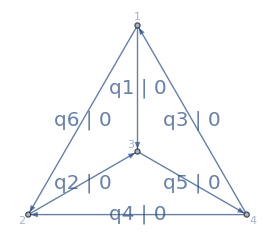

```mathematica
Vacc=DirectedGraph[{
DirectedEdge[1,3,1],
DirectedEdge[2,3,2],
DirectedEdge[3,4,5],
DirectedEdge[1,2,6],
DirectedEdge[4,2,4],
DirectedEdge[4,1,3]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Vacc=AssignSignatures[Vacc,masses-><|1->0,2->0,3->0,4->0,5->0,6->0|>,lmb->{1,2,3}];
Vacc=DirectedGraph[Vacc,VertexLabels->Automatic,ImageSize->275,GraphLayout->"TutteEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>" | "<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[Vacc]}]]
```

```mathematica
TakeSingleResidue[CFFexpr_,esurf_]:=Block[{res, newO,sortedEsurf,esurfsInTerm},
sortedEsurf=Sort[esurf];
res=Table[
<|
"Orientation"->o["Orientation"],
"Terms"->Select[Table[
esurfsInTerm=Select[t["Esurfs"],(Not[Sort[#["OSE"]]==sortedEsurf])&];
If[Length[esurfsInTerm]!=Length[t["Esurfs"]],
<|"Num"->t["Num"],"Orderings"->t["Orderings"],"Esurfs"->esurfsInTerm|>
,Null]
,{t, o["Terms"]}],Not[#===Null]&]
|>
,{o,CFFexpr}
]
]
```

```mathematica
ResidueResult=ConvertCFFFormat[TakeSingleResidue[CrossFreeFamilyLTD[Vacc,ConvertToNormalisedFormat->True],{1,2,3,4}],Vacc]
```

(<|1→-1,2→-1,3→-1,4→-1,5→1,6→-1|> | 0
<|1→-1,2→-1,3→-1,4→-1,5→1,6→1|> | 0
<|1→-1,2→-1,3→-1,4→1,5→1,6→1|> | 0
<|1→-1,2→-1,3→1,4→-1,5→1,6→-1|> | 0
<|1→-1,2→-1,3→1,4→1,5→-1,6→-1|> | 1/((OSE(3)+OSE(4)+OSE(5)) (OSE(1)+OSE(3)+OSE(6)))
<|1→-1,2→-1,3→1,4→1,5→-1,6→1|> | 1/((OSE(3)+OSE(4)+OSE(5)) (OSE(2)+OSE(4)+OSE(6)))
<|1→-1,2→-1,3→1,4→1,5→1,6→-1|> | 1/((OSE(1)+OSE(2)+OSE(5)) (OSE(1)+OSE(3)+OSE(6)))
<|1→-1,2→-1,3→1,4→1,5→1,6→1|> | 1/((OSE(1)+OSE(2)+OSE(5)) (OSE(2)+OSE(4)+OSE(6)))
<|1→-1,2→1,3→-1,4→-1,5→1,6→-1|> | 0
<|1→-1,2→1,3→1,4→-1,5→-1,6→-1|> | 0
<|1→-1,2→1,3→1,4→-1,5→1,6→-1|> | 0
<|1→-1,2→1,3→1,4→1,5→-1,6→-1|> | 0
<|1→1,2→-1,3→-1,4→-1,5→1,6→1|> | 0
<|1→1,2→-1,3→-1,4→1,5→-1,6→1|> | 0
<|1→1,2→-1,3→-1,4→1,5→1,6→1|> | 0
<|1→1,2→-1,3→1,4→1,5→-1,6→1|> | 0
<|1→1,2→1,3→-1,4→-1,5→-1,6→-1|> | 1/((OSE(1)+OSE(2)+OSE(5)) (OSE(2)+OSE(4)+OSE(6)))
<|1→1,2→1,3→-1,4→-1,5→-1,6→1|> | 1/((OSE(1)+OSE(2)+OSE(5)) (OSE(1)+OSE(3)+OSE(6)))
<|1→1,2→1,3→-1,4→-1,5→1,6→-1|> | 1/((OSE(3)+OSE(4)+OSE(5)) (OSE(2)+OSE(4)+OSE(6)))
<|1→1,2→1,3→-1,4→-1,5→1,6→1|> | 1/((OSE(3)+OSE(4)+OSE(5)) (OSE(1)+OSE(3)+OSE(6)))
<|1→1,2→1,3→-1,4→1,5→-1,6→1|> | 0
<|1→1,2→1,3→1,4→-1,5→-1,6→-1|> | 0
<|1→1,2→1,3→1,4→1,5→-1,6→-1|> | 0
<|1→1,2→1,3→1,4→1,5→-1,6→1|> | 0)

```mathematica
(*ResidueResult=ConvertCFFFormat[CrossFreeFamilyLTD[Vacc,ConvertToNormalisedFormat->True],Vacc];*)
```

```mathematica
ResidueResultEvaluated=Total[Values[ComputeSubtractionTerm[
<|
"cFFexpr"->ResidueResult,
"num"->(*(t1*t2+t1 u1 + u1 (s1 + u2))*)s1/.{
s1->2SP4[q[1],q[2]],s2->2SP4[q[3],q[4]],
t1->-2SP4[q[1],q[3]],t2->-2SP4[q[2],q[4]],
u1->-2SP4[q[1],q[4]],u2->-2SP4[q[2],q[3]]
},
"graph"->Vacc,
"dots"-><||>
|>,
(*Tri1Lnumerics*){},UVRescaling->False]]](2OSE[1])(2OSE[2])(2OSE[3])(2OSE[4])//Simplify
```

-((OSE(1)+OSE(2)+OSE(3)+OSE(4)+2 OSE(5)) (OSE(1)+OSE(2)+OSE(3)+OSE(4)+2 OSE(6)) (k1.k2-OSE(1) OSE(2)))/(2 OSE(5) (OSE(1)+OSE(2)+OSE(5)) (OSE(3)+OSE(4)+OSE(5)) OSE(6) (OSE(1)+OSE(3)+OSE(6)) (OSE(2)+OSE(4)+OSE(6)))

```mathematica
VaccNumerics=GenerateRandomSample[Vacc,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17},k3→{17/19,19/23,23/29}}

```mathematica
VaccNumerics={k1->100{0,0,1},k2->100{0,0,-1},k3->100{0,1/Sqrt[2],1/Sqrt[2]}}
```

{k1→{0,0,100},k2→{0,0,-100},k3→{0,50 √2,50 √2}}

```mathematica
VaccOSEReplacements=ComputeOSEReplacements[Vacc,{}]
```

{OSE(1):>√(k1.k1),OSE(2):>√(k2.k2),OSE(5):>√((k1+k2).(k1+k2)),OSE(6):>√((k3-k1).(k3-k1)),OSE(4):>√((k1+k2-k3).(k1+k2-k3)),OSE(3):>√(k3.k3)}

```mathematica
CommentPaperTarget=((tt^2+tt ut + ut (st + ut))/(2st tt))/.{st->2 (Sqrt[k1.k1] Sqrt[k2.k2]-k1.k2),tt->2 (Sqrt[k3.k3] Sqrt[k1.k1]+k3.k1),ut->2 (Sqrt[k3.k3] Sqrt[k2.k2]+k3.k2)};
```

```mathematica
Target=(CommentPaperTarget/.VaccNumerics)//N
Reproduced=(((ResidueResultEvaluated/.{OSE[1]:>(-OSE[2]-OSE[3]-OSE[4])})/.VaccOSEReplacements)/.VaccNumerics)//N
Target/Reproduced
```

0.59835

-0.0000585786

-10214.5

```mathematica
Series[1/(r^2 l.l+m2^2)^2 r^8 Normal[Series[1/(t^2 r^2 k.k+m^2)^2t^4,{t,Infinity,2}]]/.{t->1},{r,Infinity,0}]
```

1/((k.k)^2 (l.l)^2)+O((1/r)^1)

```mathematica
Series[1/(r^2 l.l+m2^2)^2 r^4 Normal[Series[1/(t^2 k.k+m^2)^2t^4,{t,Infinity,2}]]/.{t->1},{r,Infinity,0}]
```

(k.k-2 m^2)/((k.k)^3 (l.l)^2)+O((1/r)^1)

```mathematica
TrialNumeratorA=(qE[1]^2*qE[3]);
TrialNumeratorB=(qE[2]^2*qE[4]);
aaa=ResidueResultEvaluated=Total[Values[ComputeSubtractionTerm[
<|
"cFFexpr"->ResidueResult,
"num"->TrialNumeratorA/.{
s1->2SP4[q[1],q[2]],s2->2SP4[q[3],q[4]],
t1->-2SP4[q[1],q[3]],t2->-2SP4[q[2],q[4]],
u1->-2SP4[q[1],q[4]],u2->-2SP4[q[2],q[3]]
},
"graph"->Vacc,
"dots"-><||>
|>,
(*Tri1Lnumerics*){},UVRescaling->False]]](2OSE[1])(2OSE[2])(2OSE[3])(2OSE[4])(2OSE[5])//Simplify
bbb=ResidueResultEvaluated=Total[Values[ComputeSubtractionTerm[
<|
"cFFexpr"->ResidueResult,
"num"->TrialNumeratorB/.{
s1->2SP4[q[1],q[2]],s2->2SP4[q[3],q[4]],
t1->-2SP4[q[1],q[3]],t2->-2SP4[q[2],q[4]],
u1->-2SP4[q[1],q[4]],u2->-2SP4[q[2],q[3]]
},
"graph"->Vacc,
"dots"-><||>
|>,
(*Tri1Lnumerics*){},UVRescaling->False]]](2OSE[1])(2OSE[2])(2OSE[3])(2OSE[4])(2OSE[5])//Simplify
((aaa-bbb))//FullSimplify//Together//FullSimplify
(((aaa-bbb)/.VaccOSEReplacements)/.VaccNumerics)//Simplify//N
```

0

0

0

0.

```mathematica
VaccOSEReplacements
```

{OSE(1):>√(k1.k1),OSE(2):>√(k2.k2),OSE(5):>√((k1+k2).(k1+k2)),OSE(6):>√((k3-k1).(k3-k1)),OSE(4):>√((k1+k2-k3).(k1+k2-k3)),OSE(3):>√(k3.k3)}

```mathematica
VaccNumerics
```

{k1→{0,0,100},k2→{0,0,-100},k3→{0,50 √2,50 √2}}

```mathematica
(*TrialNumerator=(*(t1*t2+t1 u1 + u1 (s1 + u2))*)(t2);*)
(*TrialNumerator=(*(t1*t2 + t1 u1 + u1 (s1 + u2))*)(t1);*)
TrialNumerator=(t2*t2 + t2 u2 + u2 (s2 + u2));
ResidueResultEvaluated=(Total[Values[ComputeSubtractionTerm[
<|
"cFFexpr"->ResidueResult,
"num"->TrialNumerator/.{
s1->2SP4[q[1],q[2]],s2->2SP4[q[3],q[4]],
t1->-2SP4[q[1],q[3]],t2->-2SP4[q[2],q[4]],
u1->-2SP4[q[1],q[4]],u2->-2SP4[q[2],q[3]]
}(*/.{
s1->-2q[1].q[2],s2->-2q[3].q[4],
t1->-2q[1].q[3],t2->-2 q[2].q[4],
u1->-2q[1].q[4],u2->-2 q[2].q[3]
}*),
"graph"->Vacc,
"dots"-><||>
|>,
(*Tri1Lnumerics*){},UVRescaling->False]]](2OSE[1])(2OSE[2])(2OSE[3])(2OSE[4]))//FullSimplify;


CommentPaperTarget=((2 TrialNumerator/(st tt))/.{s1->st,s2->st,t1->tt,t2->tt,u1->ut,u2->ut})/.{
st->2 (Sqrt[k1.k1] Sqrt[k2.k2]-k1.k2),tt->2 (Sqrt[k3.k3] Sqrt[k1.k1]+k3.k1),ut->2 (Sqrt[k3.k3] Sqrt[k2.k2]+k3.k2)
};
(*
AA
ResidueResultEvaluated
A
(ResidueResultEvaluated/.{OSE[1]:>(-OSE[2]-OSE[3]-OSE[4])})//FullSimplify
B
*)
Target=N[CommentPaperTarget/.VaccNumerics,32]
Reproduced=N[((FullSimplify[(ResidueResultEvaluated/.{OSE[1]:>(-OSE[2]-OSE[3]-OSE[4])})]/.VaccOSEReplacements)/.VaccNumerics),32]
N[Target/Reproduced,32]
```

2.3933982822017871339873345684273

2.3933982822017871339873345684273

1.